## Genomic comparisons

I will start with a list of GenBank accession IDs. These were culled from a large list comprised of sequences I have seen in recent literature, blogs, and elsewhere, all for the purpose of comparison to 2019-nCoV. GenBank has the data for these in FASTA format. The last two lines are comprised of IDs for several of the 2019-nCoV sequences that have been placed in GenBank to date. The first of those is the initial such.

```mathematica
manyviruses={"MG772933","MG772934",
"MK211376","KJ473816","KY417145","KF294455","KY417144",
"AY395003","AY394996","AY390556","EU371564","AY394985","EU371559","AY559093","NC_004718","AY304488",
"AY502927","GU553365","EU371562","AY278488","AY274119",
"NC_005831","MF542265","KY983587","KY967357",
"AY729016","NC_006579","NC_019843.3","NC_038294",
"MN908947.3","MN938384","MN975262","MN985325","MN988713" ,"MN988668","MN994467","MN994468","MN997409","MN988669","MN996527","MN996528","MN996529","MN996530","MN996531"};
manyviruses//Length
```

44

### Importing sequences from GenBank

We obtain the sequences using a really handy function from the Wolfram Function Repository (WFR): ImportFASTA. It was written by my colleague Brendan Elli. It started out as code he wrote in response to a request I made in-house. No good deed goes unpunished. Also note that my colleague John Cassel has created a resource data object containing the 2019-nCoV examples above as well as new ones that have been more recently sequenced  (he also provided some helpful advice for this notebook). For other useful resource of 2019-nCoV genetic data please see the following Wolfram Data Repository entry:
https://datarepository.wolframcloud.com/resources/Genetic-Sequences-for-Novel-Coronavirus-2019-nCoV-from-Wuhan-China

On my machine it takes around a second to obtain each sequence. From past usage I am fairly sure this has to do with server access requirements and not sequence lengths.

```mathematica
AbsoluteTiming[vseqs=Map[ResourceFunction["ImportFASTA"],manyviruses];]
```

{46.3862,Null}

We now separate out names and genome sequences. It turns out that some sequences have a trailing repeated “A” (for adenine) and others have this removed; in particular both types appear in the 2019-nCoV set, and this is almost certainly an artifact of either sequencing protocols or perhaps decisions to remove trailing “junk”. I found that by removing it uniformly we get results that seem not to suffer from artificial discrepancies.

```mathematica
names=vseqs[[All,1,1]];
vstrings=vseqs[[All,2,1]];
shortnames=Map[StringTake[#,30]&,names];
vstrings=Map[StringReplace[#,"A"..~~ EndOfString:>""]&,vstrings];
```

The lengths are all in the ballpark of 30K nucleotides, with the exception of two (they may have been only partial sequences).

```mathematica
Map[StringLength,vstrings]
```

{29776,29706,30256,29141,29694,21477,29754,29623,29659,29756,29508,29506,29727,29711,29727,29730,29727,29644,29598,29708,29727,27553,27246,27234,27202,14886,14885,30107,30099,29870,29838,29870,29870,29870,29869,29870,29870,29870,29869,29825,29870,29852,29854,29857}

### Building a phylogenetic tree

Now we will create a phylogenetic tree, again with a handy WFR function, PhylogeneticTreePlot. I use a color scheme that is intended to group families but I do not claim to have done this without errors.

```mathematica
colors=Flatten[{ConstantArray[Brown,2],
ConstantArray[Red,5],
ConstantArray[Blue,14],
ConstantArray[Green,4],
ConstantArray[Cyan,4],
ConstantArray[Black,15]
}];
stylednames=Thread[Style[shortnames,colors]];
```

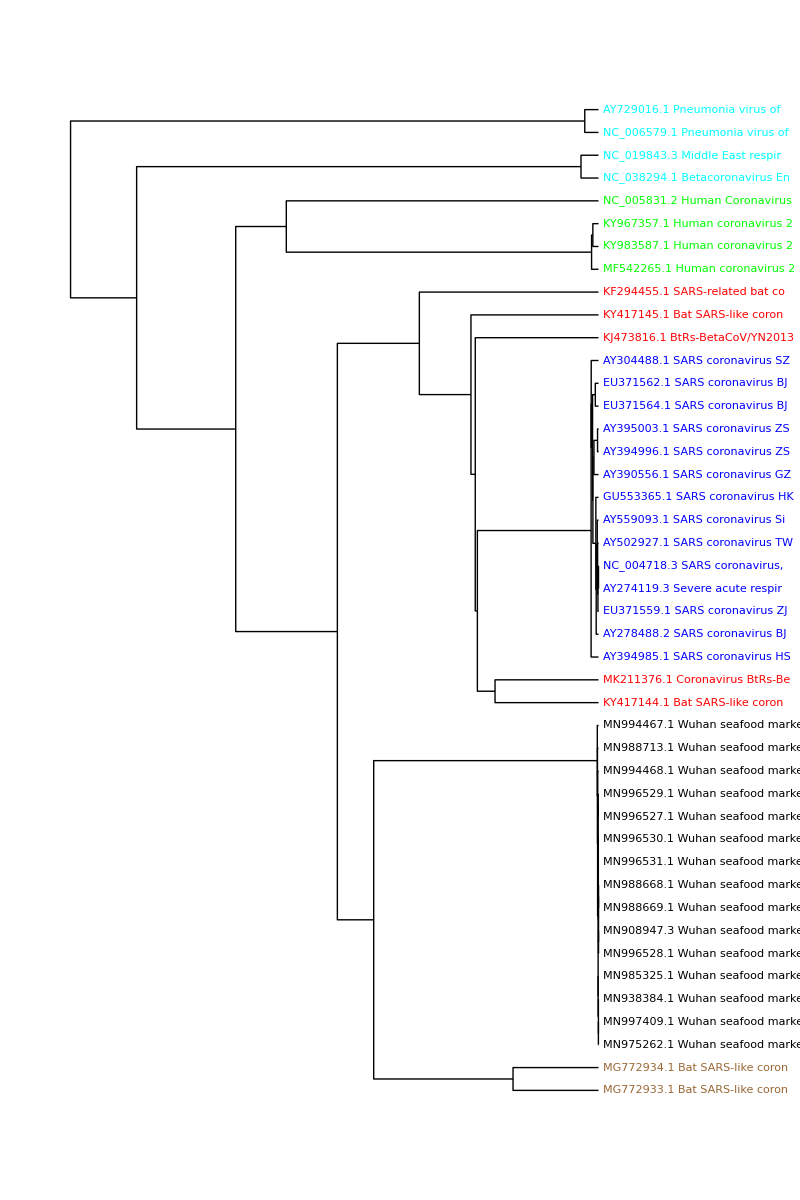

```mathematica
ResourceFunction["PhylogeneticTreePlot"][vstrings,stylednames,AspectRatio->1.5,ImageSize->800]
```

So no big surprises here. In particular this is in agreement with various analyses that have recently appeared, indicating that the 2019-nCoV has greatest similarity to the two bat SARS-like coronavirus with IDs MG772933 and MG772934 respectively.

One can of course zoom in on, say, just the 2019-nCoV samples.

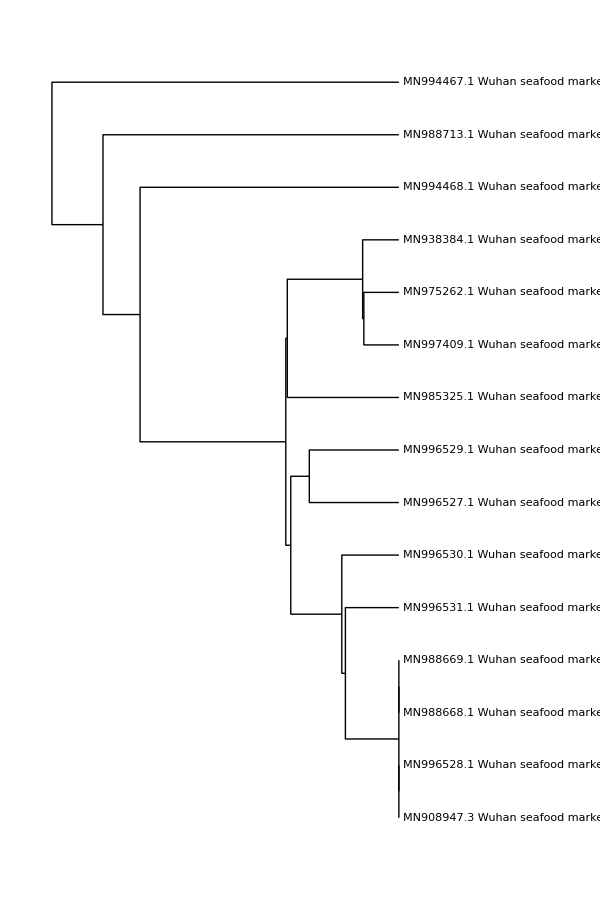

```mathematica
ResourceFunction["PhylogeneticTreePlot"][vstrings[[-15;;]],shortnames[[-15;;]],AspectRatio->1.5,ImageSize->600]
```

### Illustrating in three dimensions

One can create numeric vectors from the genome sequences, and that is in fact what PhylogeneticTreePlot does behind the scenes. I will use essentially the same code as is in the definition notebook for that function, in order to provide a different illustration of the “distances” between these viruses. (For brevity I omit it here, but see last section.) One can access the code in question by opening the definition notebook with the code below.

```mathematica
ResourceObject["PhylogeneticTreePlot"]["DefinitionNotebook"]
```

dvp57_shm32FrontEndObject[LinkObject["dvp57_shm", 3, 1]]32PhylogeneticTreePlot-definition.nbCloudObject[https://www.wolframcloud.com/obj/a692d068-a627-4dc8-a24b-fe0da4a01572]

Using this code I created a set of numeric vectors, each of length 40, for the genome sequences. They are stored a vecs2019nCoV and for convenience of data exploration I include them below.

Now we can use dimension reduction to place these in three dimensions, in a way that attempts to retain approximate distances between all pairs (this is the point of dimension reduction).

```mathematica
styled=Apply[Style,Thread[{DimensionReduce[vecsCOV,3,Method->"LatentSemanticAnalysis"],colors}],{1}];
ListPointPlot3D[styled,PlotRange->All]
```

-Graphics3D-

The (clustered) two brown points, as expected, are closest to the black 2019-nCoV cluster.  the “TSNE” method shows a somewhat different picture however.

```mathematica
styled=Apply[Style,Thread[{DimensionReduce[vecs2019nCoV,3,Method->"TSNE"],colors}],{1}];
ListPointPlot3D[styled]
```

-Graphics3D-

I am somewhat partial to a method not built into DimensionReduce, known as Multidimensional Scaling. So partial, in fact, that I put it into the WFR.

```mathematica
styled=Apply[Style,Thread[{ResourceFunction["MultidimensionalScaling"][vecsCOV,3],colors}],{1}];
ListPointPlot3D[styled]
```

-Graphics3D-

This gave a plot that is not too different from the latent semantic analysis method. The Properties and Relations section of the definition notebook gives an indication of why they are similar (in brief: both are based on the Singular Values Decomposition from linear algebra).

## Locating possible “hot spots” on a genome sequence

This section is, uhm, on the “tentative” side. I simply lack the genetics background to assert that the following analysis carries much meaning from a biological point of view. But it does show tools that can be deployed regardless. (Strictly speaking, I also am lacking in genetic expertise for the preceding genome comparison section, but there at least I have the benefit of having developed tools and tested them on several benchmark data sets.)

The idea we pursue is as follows. It is known that coding sections (exons) of genomes correlate heavily with a periodicity of three. Of course this forces the question of how to gauge periodicity. It turns out that several methods are available for this purpose. I will show two, and we will see that they are in rough agreement. It should be noted that these are crude and, at best, accurate to tens of nucleotides. With emphasis on “at best”. For both methods we need to form a signal from a genome sequence. One method is fairly well known and allows us to apply basic Fourier methods to get a frequency, from which we can then derive a period. Of course there can be multiple large frequencies, and corresponding periodicities. But the length three period, when it appears, is dominant, and we will use that to advantage.

We illustrate with the first of the 2019-nCoV genomes in our list.

```mathematica
virus=vstrings[[-15]];
```

In order to localize “hot” areas (that is, regions that show the three-periodicity), we will segment into overlapping substrings of length 500, with a spacing of 100. When we locate substrings of interest we will merge any that have centers falling strictly within the range of prior substrings of interest.

```mathematica
sublength=500;
vsubstrings=StringPartition[virus,sublength,Ceiling[sublength/5]];
```

### Method 1: construct sequences in 3D and compute the Fourier spectra

The idea is to regard each of the four nucleotides as occupying a vertex of a regular tetrahedron centered at the origin. So each gets associated to a point in 3-space. The array of three dimensional values thus created can then be analyzed for frequency information using Fourier.

```mathematica
tetverts=N[{{1,0,-1/2},{-1/2,Sqrt[3]/2,-1/2},{-1/2,-Sqrt[3]/2,-1/2},{0,0,Sqrt[2]-1/2}}];
repRule=Thread[{"A","T","C","G"}->tetverts];
viralseqs=Map[Transpose[Characters[#]/.repRule/._String->Nothing]&,vsubstrings];
```

We get the three Fourier sequences for each of these substrings.

```mathematica
fts=Map[Fourier,viralseqs,{2}];
```

Now sum absolute values for the three sequences (one per dimension) obtained from each substring. We remove the first components to avoid an artificially high DC component.

```mathematica
vals=Map[Total[Abs[#[[All,2;;]]]]&,fts];
```

It might be instructive to see some of the plots these produce. Those with clear three-periodicities will be seen to have spikes at 1/3 and 2/3 distance along the x axis.

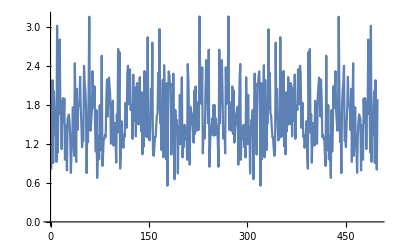
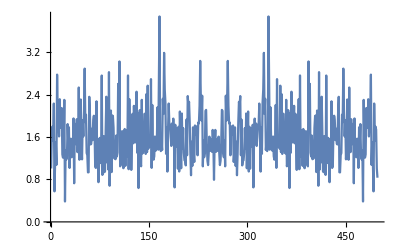
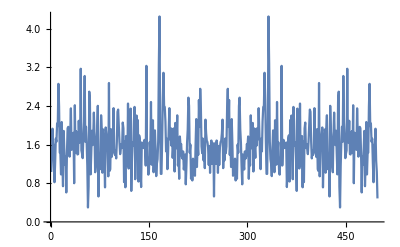
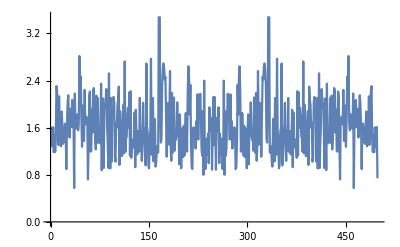
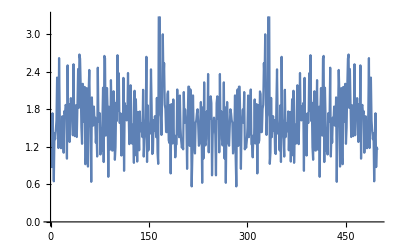
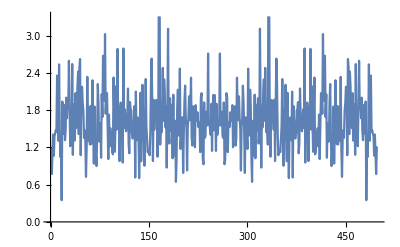
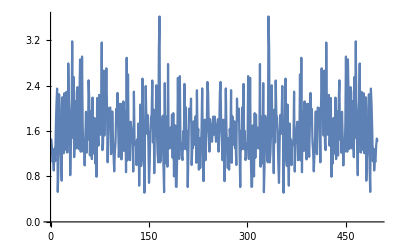
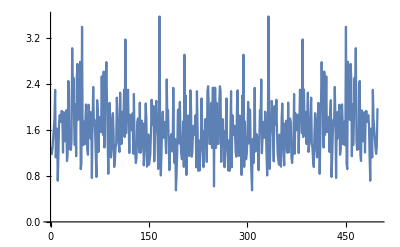

```mathematica
Table[ListPlot[vals[[j]],Joined->True],{j,10}]
```

Noting that the spikes of interest are both the largest in their respective plots, and also tend to exceed 3.3 or so on the y axis, we use this to locate the substrings of interest. We compute the positions of the middles (strictly speaking,1/2 position to the left since the lengths are even).

```mathematica
middles=Reap[periods=Table[
{max,maxpos}=TakeLargest[vals[[j]]->{"Element","Index"},1][[1]];
If[max>3.3&&(165≤maxpos≤168||332≤maxpos≤335),Sow[100*(j-1)+250]]
,{j,Length[vals]}];][[2,1]]
```

{350,450,550,650,750,850,950,1350,1450,1550,1650,1750,1850,1950,2450,2650,2750,2850,2950,3050,3150,3250,3350,3450,3550,3650,3750,3850,3950,4050,4150,4250,4350,4550,4650,4750,4850,4950,5050,5850,5950,6050,6150,6250,6350,6450,6550,6650,6750,6850,6950,7050,7150,7250,7650,7750,7850,7950,8050,8150,8250,8350,8450,8650,8750,8850,8950,9050,9150,9250,9350,9450,10050,10150,10250,10450,10550,10650,10750,10850,11150,11350,12050,12150,12250,12350,12450,12550,12650,12750,12850,12950,13050,13150,13250,13550,13650,13750,14550,14650,14750,14850,14950,15050,15150,15250,15350,15650,15750,15850,15950,16450,16550,16650,16750,16950,17150,17250,17350,17850,18050,18150,18250,18350,18450,18650,18750,18850,18950,19050,19350,19450,19550,19650,19750,19850,19950,20050,20150,20250,20850,20950,21050,21150,21650,21850,21950,22050,22150,22250,22350,22450,22550,22650,22750,22850,22950,23050,23150,23250,23350,23450,23550,23650,23750,23850,23950,24150,24250,24350,24450,24550,24850,24950,25050,25750,25950,26050,26150,27050,27150,28350,28450,28550,28650,28750,28850,28950,29050}

The code below will “clump” these into longer runs, when later middle points fall inside prior intervals.

```mathematica
hotRuns[middles_,sublength_,step_]:=Reap[Module[
{start=middles[[1]],jump=sublength/2,end,j},
end=start+jump;
j=1;
While[j<Length[middles],
j++;
If[middles[[j]]-jump<end,
end+=step,
Sow[{start-jump,end}];start=middles[[j]];end=start+jump
]];
Sow[{start-jump,end}]
]][[2,1]]
```

```mathematica
hotRuns[middles,sublength,100]
```

{{100,1900},{2200,5100},{5600,8400},{8400,9700},{9800,11100},{11100,11600},{11800,13800},{14300,16000},{16200,17400},{17600,19100},{19100,20500},{20600,21400},{21400,24600},{24600,25300},{25500,26300},{26800,27400},{28100,29300}}

### Method 2: Irregular periodograms find common gap frequencies

Here again we use a WFR function, this one being IrregularPeriodogram. I follow an example in the documentation for that function, so again I include the line for opening the definition notebook/

```mathematica
ResourceObject["IrregularPeriodogram"]["DefinitionNotebook"]
```

The idea is to find locations of certain dinucleotides, specifically “AA”, ”AT”, and ”TT”. There is a large body of literature indicating that these in particular show three-periodicity. Actually one usually works with related trimers or tetramers, but the relatively small substring lengths warrant using the dinucleotides to get sufficient data. We work with gap lengths between these dinucleotides, and try to assess strong frequencies from that data. The three-periodic substrings will appear as having strong frequency components at 2π/3 and 4π/3. To cut back on noise in assessing common gaps, we remove those that only appear one time in a given substring.

```mathematica
at4="AA"|"AT"|"TT";
posnlists=Map[StringPosition[#,at4][[All,1]]&,vsubstrings];
pdiffs=Table[Outer[Subtract,posnsj,posnsj],{posnsj,posnlists}];
pdiffs2=Map[DeleteCases[Flatten[#],aa_/;(aa≤2)]&,pdiffs];
tallies=Map[Tally,pdiffs2];
talliesS0=Map[ReverseSortBy[#,Last]&,tallies];
talliesS=Map[DeleteCases[#,{_,1}]&,talliesS0];
```

Now compute periodograms based on these gaps. Note that while we compute these at regular intervals, the inputs are not regular and so the irregular periodogram really is warranted. We compute over a range that begins well before 2π/3 so that we can remove any that might be large near that value but have larger spikes earlier.

```mathematica
pgrams=Table[{timesC,valsC0}=Transpose[talliesS0[[j]]];
valsC=valsC0-Mean[N@valsC0];
Table[ResourceFunction["IrregularPeriodogram"][w,timesC,valsC,Method->"Deeming"],{w,1.1,2.4,.01}],
{j,Length[talliesS]}];
```

Again it is instructive to see some plots.

We will determine candidates

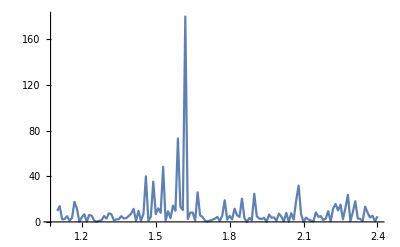
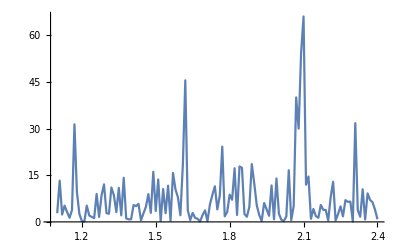
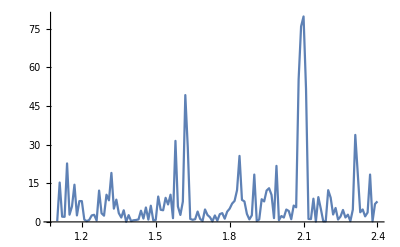
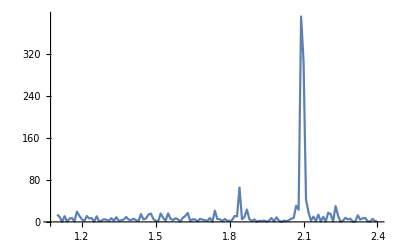
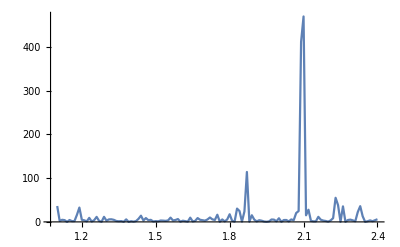
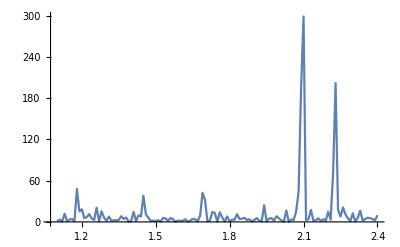
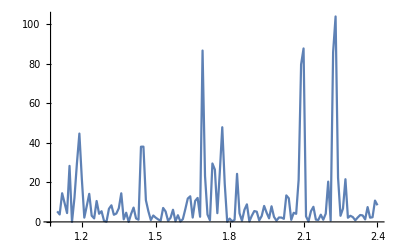
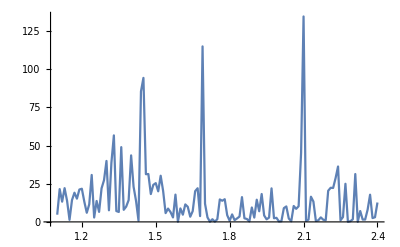

```mathematica
freqs=Range[1.1,2.4,.01];
Table[ListPlot[Transpose@{freqs,pgrams[[j]]},Joined->True,PlotRange->All],{j,10}]
```

Several show strong spikes in the frequency range of interest, and they tend to exceed 150. We use that to determine the “keepers”.

```mathematica
candidateHotStringQ[freqs_,vals_]:=
2.00≤freqs[[FirstPosition[vals,Max[vals]][[1]]]]≤2.20&&Max[vals]>150
```

```mathematica
hotList=Map[candidateHotStringQ[freqs,#]&,pgrams];
middlePosns=100*(Range[Length[pgrams]]-1)+250;
hotMiddles=Pick[middlePosns,hotList]
```

{550,650,750,1450,1550,1650,2850,2950,3050,3150,3250,3350,3450,3550,3650,3750,3850,3950,4750,4850,4950,6050,6250,6350,6450,6550,8050,8150,8250,8350,8450,14750,14850,15750,18650,18850,18950,19650,19850,19950,20050,20150,20250,20350,20450,21750,24150,24450,24550,24650,25550,25850,26150}

Again we clump these.

```mathematica
hotRuns[hotMiddles,sublength,100]
```

{{300,1000},{1200,1900},{2600,4200},{4500,5200},{5800,6700},{7800,8700},{14500,15100},{15500,16000},{18400,19100},{19400,20600},{21500,22000},{23900,24700},{25300,25900},{25900,26400}}

This tends to be a more spare list than that from method 1. All the same, they do appear to have considerable overlap.

### Alignment-free alignment

Genome alignment is done in order to either connect subsequences, or to compare one genome to another to check for possible relationships. It is typically performed using string processing based methods, and these can be expensive. In this section i will show a method that falls very much within the “alignment-free” family of genome analysis. But we deploy it in a way that actually can inform alignment possibilities, by narrowing the search ranges.

The idea is as follows. From the phylogenetic tree in the first section we already know that the 2019-nCoV appears to be most closely related to two bat SARS-like coronaviruses. We will compare the same 2019-nCoV genome used in the prior section to one of those two similar ones. As in the last section we again use substrings of length 500. For this work I do require the code used in the WFR function PhylogeneticTreePlot, so this will be a bit more elaborate from the code point of view. One of the tools is itself a WFR function, FCGRImage. That function actually creates images from DNA strings. Since we really want the underlying matrices we convert back using ImageData.

#### Support code

```mathematica
srules={"U"->"T",Except[Characters["ACGT"]]->""};
chars={"A","T","G","C"};
replace=Dispatch[Thread[chars->{{0,0},{0,1},{1,1},{1,0}}]];
```

```mathematica
processNucleotideString[chars_,dim_,freq_]:=Module[
{fcgr=ImageData[ResourceFunction["FCGRImage"<>][chars,dim]],ftt},
If[Max[fcgr]==0,
{}
,(*else*)
fcgr=(fcgr/N[Max[fcgr]])^(1/5);
ftt=Flatten[FourierDCT[fcgr-Mean[Flatten[fcgr]],4][[1;;freq,1;;freq]]];
ftt-Mean[ftt]
]
]
```

```mathematica
trainVectorsProcess[ivecs_,vals_,keep_]:=
Module[
{uu,ww,vv,udotw,norms},
{uu,ww,vv}=
SingularValueDecomposition[ivecs,keep];
udotw=uu.ww;
norms=Map[Sqrt[#.#]&,udotw];
udotw=udotw/norms;
udotw=Join[udotw,Transpose[{Log[norms]}],2];
{Nearest[udotw->vals],vv}]

testVectorsProcess[ivecs_,vv_]:=
Module[
{tdotv,norms},
tdotv=ivecs.vv;
norms=Map[Sqrt[#.#]&,tdotv];
tdotv=tdotv/norms;
tdotv=Join[tdotv,Transpose[{Log[norms]}],2];
tdotv]
```

#### Application to our two genomes

The method proceeds as follows. We preprocess both sets of substrings, first obtaining the FCGR arrays and then reducing dimension with the discrete Fourier Cosine Transform (using FourierDCT). The older genome is the “reference” set and the 2019-nCoV processed strings will be our “test” set. A next step is to take the reference processed vectors and further reduce dimension using the Singular Values Decomposition (SVD for short, implemented as a function called, not surprisingly, SingularValuesDecomposition). We return  both a lookup function created using Nearest, and the right side conversion matrix from the SVD. this latter is needed in order to also reduce dimensions for the test vectors.

```mathematica
referenceVirus=vstrings[[1]];
referenceSubstrings=StringPartition[referenceVirus,sublength,Ceiling[sublength/5]];
```

```mathematica
dim=7;
freq=30;
keep=40;
fttsRefVirus=Map[Developer`ToPackedArray[processNucleotideString[#,dim,freq]]&,referenceSubstrings];
{nf,vv}=trainVectorsProcess[fttsRefVirus,Range[Length[fttsRefVirus]],keep];
testVecs=testImageProcess[Map[Developer`ToPackedArray[processNucleotideString[#,dim,freq]]&,vsubstrings],vv];
```

The processing from here is straightforward. Each text vector corresponds to a substring in the test genome sequence. We look up the “closest” dimension-reduced vector from the reference genome. Sections that tend to align well will be recognized because contiguous chunks in the test genome will have, as closest neighbors, approximately consecutive runs in the reference set.

```mathematica
neighbors=Flatten[nf[testVecs]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,20,20,21,22,23,24,25,26,26,27,28,29,31,32,34,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,50,52,52,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,79,81,82,83,84,84,85,87,88,90,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,113,115,116,117,118,119,120,121,122,122,124,125,126,127,128,128,130,131,132,133,134,135,136,48,48,48,48,190,142,144,145,145,146,147,148,149,150,151,151,153,153,155,158,158,158,159,160,161,161,161,164,165,167,168,168,169,170,170,172,172,173,174,176,177,178,179,180,180,182,183,184,185,185,189,190,189,190,190,191,192,195,195,196,196,198,198,198,199,202,203,204,205,206,207,207,209,210,211,212,213,213,215,215,220,69,69,218,220,220,224,226,226,227,69,227,227,227,227,231,231,233,234,235,237,237,238,240,240,241,241,243,244,244,246,247,248,249,250,251,252,253,254,255,256,257,259,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,278,280,281,282,284,284,285,286,287,288,289,290,291,293,293}

I will defer on writing yet more code to do a detailed associating of consecutive runs from one to similar runs from the other. By eye one can observe that these initially seem to align quite well. We do see that fairly late in the set, vector 69 from the reference set is nearest neighbor to a few in the test set.

```mathematica
Flatten[Position[neighbors,69]]
```

{69,218,219,227}

The first such is of course expected. The later ones indicate that there is something of a gap in the test set, where matches to the reference genome are out of alignment. We also see that there are a few matches to chunk 227, just before and after the final match to chunk 69. We’ll chek their locations.

```mathematica
Flatten[Position[neighbors,227]]
```

{226,228,229,230,231}

This indicates that the sequences are not only approximately back in alignment, but that they seem to be so at the same positions in the respective genome sequences.

For those interested in the underlying method,  the reference is:
D. L. Alignment-free genomic sequence comparison using FCGR and signal processing. BMC Bioinformatics 20:742 (2019). DOI: 10.1186/s12859-019-3330-3 (handy link)

## Final remarks

I showed a few tools of the in Mathematica and the Wolfram Function Repository that one can use for genome analysis. These were applied to timely examples from the recent 2019 novel coronavirus. As should be obvious, I focused, perhaps to a shameless extent, on methodologies with which I am quite familiar. I hope these are applicable to work other people are doing. I also hope others will consider contributing their own work to this forum and, if applicable, to the WFR.